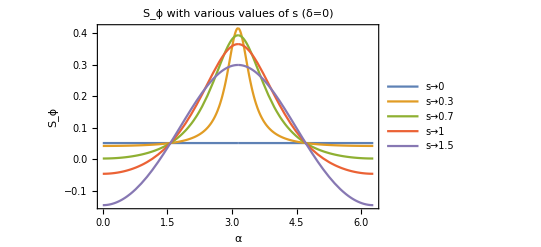

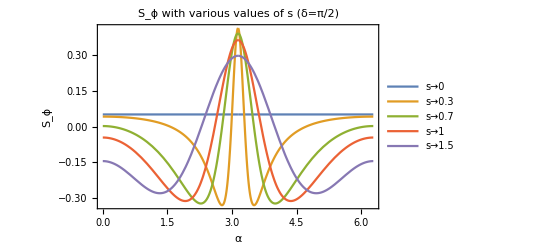

```mathematica
ClearAll;
ClearAll["`*", Subscript, Derivative];
ClearAll["Global`*",Derivative,Subscript];
β= (-s )(Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]);
NN=1/(√2)(1+Abs[A]^2+ (1-Abs[A]^2)(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2) )^(-1/2);
Subscript[Q, 1]= 2 Abs[NN]^2((Conjugate[A]+ A )s/2+(Conjugate[A]- A ) Subscript[P, 1]);(*(a)*)
Subscript[P, 1]= Subscript[R, 1]+s Subscript[R, 2]+s/2 Subscript[R, 3];
Subscript[R, 1]=( β Cosh[r]( β^2 ⅇ^(-ⅈ θ) Coth[r]+3 ))ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 2]=(β^2 ⅇ^(-ⅈ θ) Coth[r]+1)ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 3]=(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2);
Subscript[Q, 2]=2 Abs[NN]^2((1+ Abs[A]^2 )(3/2 ⅇ^(ⅈ θ) Sinh[2r]+s^2/4)+(1-Abs[A]^2)Subscript[P, 2] );(*<a^2>*)
Subscript[P, 2]=Subscript[R, 4]+s Subscript[R, 1]+s(Subscript[R, 1]+s Subscript[R, 2])+s^2/4 Subscript[R, 3];
Subscript[R, 4]=(β^2 Cosh[r]^2( β^2 ⅇ^(-ⅈ θ)Coth[r]+6 )+3/2 ⅇ^(ⅈ θ)Sinh[2r])ⅇ^(-1/2 Abs[β]^2);
Subscript[Q, 3]=2 Abs[NN]^2((  1+ Abs[A]^2 )(1+3 Sinh[r]^2+s^2/4)+(1-Abs[A]^2)Subscript[P, 3]);
Subscript[P, 3]=Subscript[R, 5]+s Subscript[R, 6]+s/2(Subscript[R, 6]+s Subscript[R, 7]+Subscript[R, 1]+s Subscript[R, 2])+s^2/4 Subscript[R, 3];
Subscript[R, 5]=(β^2 ⅇ^(-ⅈ θ) Cosh[r](Coth[r]Cosh[r]+5Sinh[r]+β^2 ⅇ^(-ⅈ θ)Cosh[r]) +1+3 Sinh[r]^2 )ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 6]=β ⅇ^(-ⅈ θ) ( (1+3 Sinh[r]^2)/Sinh[r]+β^2 ⅇ^(-ⅈ θ)Cosh[r] )ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 7]=ⅇ^(-ⅈ θ)(Coth[r]+β^2 ⅇ^(-ⅈ θ))ⅇ^(-1/2 Abs[β]^2);
SQ=Subscript[W, 2]-( Subscript[W, 1])^2-1/2(*Squeezing parameter Subscript[S, θ] = <Subscript[X, θ]^2>-<Subscript[X, θ]>^2-1/2 *);
Subscript[W, 1]= √2 Re[Subscript[Q, 1] ⅇ^(-ⅈ ϕ)];(*where Subscript[X, 1] = <Subscript[X, θ]> =1/(√2) (<a>ⅇ^(-ⅈ θ)+<a^+>ⅇ^(ⅈ θ))*)
Subscript[W, 2]=1/2(2Re[ Subscript[Q, 2] ⅇ^(-2ⅈ ϕ)]+2 Subscript[Q, 3]+1);(*where Subscript[X, 2] = <Subscript[X, θ]^2> =1/2(2Re[<a^2>ⅇ^(-2ⅈ θ)]+2<a^+a>+1)=1/2(2Re[Subscript[Q, 2]*ⅇ^(-2ⅈ θ)]+2 Subscript[Q, 3]+1) *)
A=ⅇ^(ⅈ δ) Tan[α/2];
θ=0 ;
r=0.5;
range2={0,0.3,0.7,1,1.5};
Plot[Evaluate[SQ/.{s->range2,ϕ->π/2,δ->0}],{α,0,2π},PlotRange->All,PlotLabel->HoldForm[Subscript[S, ϕ] with various values of s (δ=0) ],PlotLegends->Placed[StringForm["s→``",#]&/@range2,{Right,Top}],FrameLabel->{"α","S_ϕ"},PlotRange->Full,Frame->True]
Plot[Evaluate[SQ/.{s->range2,ϕ->π/2,δ->π/2}],{α,0,2π},PlotRange->All,PlotLabel->HoldForm[Subscript[S, ϕ] with various values of s  (δ=π/2)],PlotLegends->Placed[StringForm["s→``",#]&/@range2,{Right,Top}],FrameLabel->{"α","S_ϕ"},PlotRange->Full,Frame->True]
```